```mathematica
(* Define solution *)
r2= x^2+y^2;
theta = ArcTan[x, y];
factor = -P / 4 / Pi / mu;
nu = lam / 2/(lam+mu);
kappa =3-4nu;
u = factor* ((kappa - 1)*theta + 2x y/r2) // Simplify
v = factor* (-(kappa + 1)*Log[r2]/2 +(y^2-x^2)/r2) // Simplify
```

-(P ((2 x y)/(x^2+y^2)+(2 mu ArcTan[x,y])/(lam+mu)))/(4 mu π)

-(P ((-x^2+y^2)/(x^2+y^2)-((lam+2 mu) Log[x^2+y^2])/(lam+mu)))/(4 mu π)

```mathematica
(* Check solution *)
uu={u,v};
(lam + mu)Grad[Div[uu,{x,y}],{x,y} ]+mu Laplacian[uu,{x,y}] // FullSimplify
```

{0,0}

```mathematica
(* Derivation from polar solution found on Wikipedia *)
ur = factor((kappa-1) theta Cos[theta] +Sin[theta]-(kappa+1)Log[r2] /2Sin[theta]);
ut = factor((kappa-1) theta Sin[theta] +Cos[theta]+(kappa+1)Log[r2]/2Cos[theta]);

ux = ur Cos[theta] + ut Sin[theta] // FullSimplify;
uy = ur Sin[theta] - Cos[theta] ut // FullSimplify;

{u,v} == {ux,uy}// Simplify
```

True

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{lam→5.26161×10^10,mu→2.71053×10^10,P→5000000000}

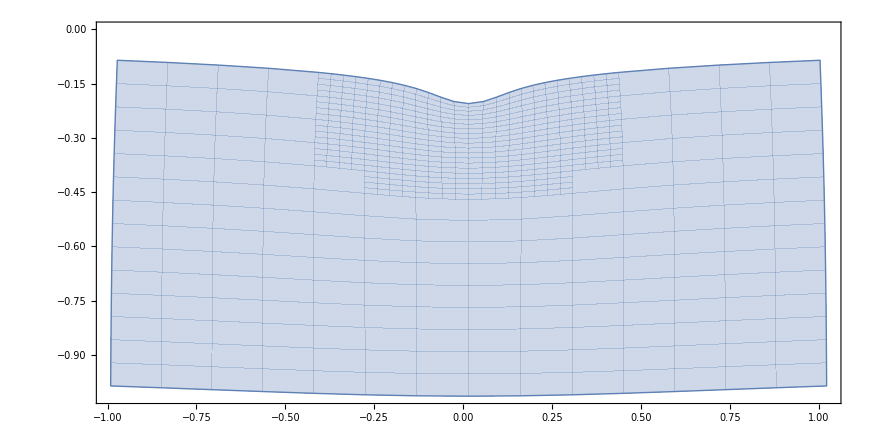

```mathematica
(* Plot solution *)
data = First@Solve[{mu(3 lam + 2mu)/(lam+mu) == 72.1 10^9,lam/2/(lam+mu)==0.33},{lam,mu}];
data = Join[data, {P->500 10^7}]
ParametricPlot[{x+u,y+v}/.data,{x,-1,1},{y,-0.1,-1}]
```